# grid and integration

## 1. Global constants and basic functions

```mathematica
hbar=1.0545718176461565*10^-27;
e=4.803204712570263*10^(-10);
me=9.1093837015*10^(-28);
mp=1.67262192369*10^-24;
A=1;Z=1;Ye=1;
kb=1.380649*10^(-16);
kev2erg=1.6021766339999998*10^-9;
c=29979245800.0;
σT=8*π/3*e^4/(c^4 me^2);
κT=σT/mp;
G=6.674299999999999*10^-8;
Ms=1.988409870698051*10^33;
km=10^5;
αF=e^2/(hbar c);
BQ=me^2*c^3/e/hbar;
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linearspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];
C0[a_]:=1/a-Exp[a]*ExpIntegralE[1,a];
C1[a_]:=(1+a)*Exp[a]*ExpIntegralE[1,a]-1;
radian[x_]:=x/180*π;
Planck[Es_,T_]:=2*hbar*2*π*(Es*kev2erg/hbar/2/π)^3/c^2*1/(Exp[(Es*kev2erg)/(kb*T)]-1);
```

## Temperature profile

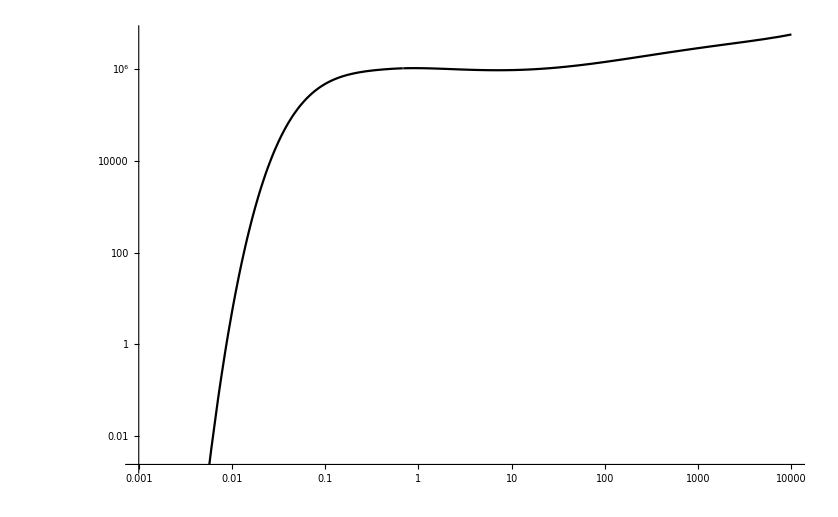

```mathematica
temperature[τ_]:=Module[{τmid,x},
τmid=0.683;
a1=0.00828;
a2= 0.0614;
a3=-0.304;
a4=0.266;
a5= -0.0719;
a6=0.00652;
b3=-0.313;
b4=−0.374;
b5=−0.612;
b6=−0.0234;
x=Log[10,τ]-Log[10,τmid];
Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}]];
LogLogPlot[temperature[τ],{τ,0.001,10^4},Background->White,PlotTheme->"Monochrome"]
```

## Scatter opacity

```mathematica
Aint[Es_,B_,τ_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,ri,ϵp,ηp,g,ϵ,η,βi,K1i,K2i,Kz1i,Kz2i,ep1i,em1i,ep2i,em2i,e01i,e02i,Ap1,Am1,A01,Ap2,Am2,A02,Ap,Am,A0,ρ,x,T,Mns,Rns,gns,τmid,γeiL,γeip,y1,y2,γre,γri,gl,gp,ϵpg,ϵmg},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
γre=9.5*10^-6*Es/1;
γri=5.2*10^-9*Z^2/A*Es/1;
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*C1[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*2*y2*Exp[2x1]C0[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
γeiL=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5 Es^2)*(1-Exp[-Ec/(kb*T)])*gl;
γeip=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5 Es^2)(1-Exp[-Ec/(kb*T)])*gp;
ϵpg=1-(ve*(1+I * γri)+vi*(1+I*γre))/((1+I*γre+ue^0.5)(1+I*γri-ui^0.5)+I*γeiL);
ϵmg=1-(ve*(1+I * γri)+vi*(1+I*γre))/((1+I*γre-ue^0.5)(1+I*γri+ui^0.5)+I*γeiL);
ϵp=1/2(ϵpg+ϵmg);
g=1/2(ϵpg-ϵmg);
ηp=1-ve/(1+I*(γeip+γre))-vi/(1+I*(γeip+γri));

ϵ=ϵp+a-1;
η=ηp+a+q-1;

ri=1+m/a Sin[θ]^2;
βi=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θ]^2/Cos[θ];
K1i=βi(1-(1+ri/βi^2)^(1/2));
K2i=βi(1+(1+ri/βi^2)^(1/2));
Kz1i=(-((ϵp-ηp-q)*Sin[θ]Cos[θ]K1i + g * Sin[θ]))/(ϵp*Sin[θ]^2+(ηp+q)Cos[θ]^2+a-1);

Kz2i=(-((ϵp-ηp-q)*Sin[θ]Cos[θ]K2i + g * Sin[θ]))/(ϵp*Sin[θ]^2+(ηp+q)Cos[θ]^2+a-1);
ep1i=Abs[1+K1i*Cos[θ]+Kz1i*Sin[θ]]^2/(2(1+Abs[K1i]^2+Abs[Kz1i]^2));
ep2i=Abs[1+K2i*Cos[θ]+Kz2i*Sin[θ]]^2/(2(1+Abs[K2i]^2+Abs[Kz2i]^2));
em1i=Abs[1-(K1i*Cos[θ]+Kz1i*Sin[θ])]^2/(2(1+Abs[K1i]^2+Abs[Kz1i]^2));
em2i=Abs[1-(K2i*Cos[θ]+Kz2i*Sin[θ])]^2/(2(1+Abs[K2i]^2+Abs[Kz2i]^2));
e01i=Abs[K1i * Sin[θ]-Kz1i*Cos[θ]]^2/(1+Abs[K1i]^2+Abs[Kz1i]^2);
e02i=Abs[K2i * Sin[θ]-Kz2i*Cos[θ]]^2/(1+Abs[K2i]^2+Abs[Kz2i]^2);
Ap=NIntegrate[3/4*Sin[θ]*(ep1i+ep2i),{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
Am=NIntegrate[3/4*Sin[θ]*(em1i+em2i),{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
A0=NIntegrate[3/4*Sin[θ]*(e01i+e02i),{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
Ap2=NIntegrate[3/4*Sin[θ]*ep2i,{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];Am2=NIntegrate[3/4*Sin[θ]*em2i,{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
A02=NIntegrate[3/4*Sin[θ]*e02i,{θ,0,π},WorkingPrecision->10,PrecisionGoal->6];
Ap1=Ap-Ap2;
Am1=Am-Am2;
A01=A0-A02;
{Ap1,Ap2,Am1,Am2,A01,A02}
]
```

```mathematica
Aint[2,5*10^14,100]
```

{0.752648439,0.2462695556,0.747350298,0.2515739948,1.28×10^-6,1.002156432}

```mathematica
scatteropacity[Es_,B_,τ_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,gl,gp,ωci,τmid,x,T,ρ,Mns,Rns,gns,γeiL,γeip,y1,y2,γre,γri,ϵpg,ϵmg,γep,γem,γe0,γip,γim,γi0,κs1e1,κs1i1,κs2e1,κs2i1,κs11,κs12,κs1e2,κs1i2,κs2e2,κs2i2,κs21,κs22},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
γre=9.5*10^-6*Es/1;
γri=5.2*10^-9*Z^2/A*Es/1;
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*C1[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*2*y2*Exp[2x1]C0[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
γeiL=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5 Es^2)*(1-Exp[-Ec/(kb*T)])*gl;
γeip=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5 Es^2)(1-Exp[-Ec/(kb*T)])*gp;
ϵpg=1-(ve*(1+I * γri)+vi*(1+I*γre))/((1+I*γre+ue^0.5)(1+I*γri-ui^0.5)+I*γeiL);
ϵmg=1-(ve*(1+I * γri)+vi*(1+I*γre))/((1+I*γre-ue^0.5)(1+I*γri+ui^0.5)+I*γeiL);
ϵp=1/2(ϵpg+ϵmg);
g=1/2(ϵpg-ϵmg);
ηp=1-ve/(1+I*(γeip+γre))-vi/(1+I*(γeip+γri));

ϵ=ϵp+a-1;
η=ηp+a+q-1;

β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ep1=Abs[1+K1*Cos[θb]+Kz1*Sin[θb]]^2/(2(1+Abs[K1]^2+Abs[Kz1]^2));
ep2=Abs[1+K2*Cos[θb]+Kz2*Sin[θb]]^2/(2(1+Abs[K2]^2+Abs[Kz2]^2));
em1=Abs[1-(K1*Cos[θb]+Kz1*Sin[θb])]^2/(2(1+Abs[K1]^2+Abs[Kz1]^2));
em2=Abs[1-(K2*Cos[θb]+Kz2*Sin[θb])]^2/(2(1+Abs[K2]^2+Abs[Kz2]^2));
e01=Abs[K1 * Sin[θb]-Kz1*Cos[θb]]^2/(1+Abs[K1]^2+Abs[Kz1]^2);
e02=Abs[K2 * Sin[θb]-Kz2*Cos[θb]]^2/(1+Abs[K2]^2+Abs[Kz2]^2);
γep=γeiL+γre;
γem=γeiL+γre;
γe0=γeip+γre;
γip=me/mp γeiL+γri;
γim=me/mp γeiL+γri;
γi0=me/mp γeip+γri;
κs1e1=Ye*κT*(((1+ue^0.5)^2+γep^2)^-1 ep1*Ap1+((1-ue^0.5)^2+γem^2)^-1 em1*Am1+((1+0*ue^0.5)^2+γe0^2)^-1 e01*A01);
κs1i1=((Z^2 me)/(A mp))^2*κT/A*(((1-ui^0.5)^2+γip^2)^-1 ep1*Ap1+((1+ui^0.5)^2+γim^2)^-1 em1*Am1+((1+0*ui^0.5)^2+γi0^2)^-1 e01*A01);
κs11=κs1e1+κs1i1;

κs1e2=Ye*κT*(((1+ue^0.5)^2+γep^2)^-1 ep1*Ap2+((1-ue^0.5)^2+γem^2)^-1 em1*Am2+((1+0*ue^0.5)^2+γe0^2)^-1 e01*A02);
κs1i2=((Z^2 me)/(A mp))^2*κT/A*(((1-ui^0.5)^2+γip^2)^-1 ep1*Ap2+((1+ui^0.5)^2+γim^2)^-1 em1*Am2+((1+0*ui^0.5)^2+γi0^2)^-1 e01*A02);
κs12=κs1e2+κs1i2;

κs2e1=Ye*κT*(((1+ue^0.5)^2+γep^2)^-1 ep2*Ap1+((1-ue^0.5)^2+γem^2)^-1 em2*Am1+((1+0*ue^0.5)^2+γe0^2)^-1 e02*A01);
κs2i1=((Z^2 me)/(A mp))^2*κT/A*(((1-ui^0.5)^2+γip^2)^-1 ep2*Ap1+((1+ui^0.5)^2+γim^2)^-1 em2*Am1+((1+0*ui^0.5)^2+γi0^2)^-1 e02*A01);
κs21=κs2e1+κs2i1;

κs2e2=Ye*κT*(((1+ue^0.5)^2+γep^2)^-1 ep2*Ap2+((1-ue^0.5)^2+γem^2)^-1 em2*Am2+((1+0*ue^0.5)^2+γe0^2)^-1 e02*A02);
κs2i2=((Z^2 me)/(A mp))^2*κT/A*(((1-ui^0.5)^2+γip^2)^-1 ep2*Ap2+((1+ui^0.5)^2+γim^2)^-1 em2*Am2+((1+0*ui^0.5)^2+γi0^2)^-1 e02*A02);
κs22=κs2e2+κs2i2;
{κs11,κs12,κs21,κs22}
]
```

```mathematica
{Ap1,Ap2,Am1,Am2,A01,A02}=Aint[1,5*10^14,100]
scatteropacity[0.01,5*10^14,100,π/100]
```

{0.750161076,0.2408407168,0.74983892,0.2411648799,4.×10^-9,1.017994403}

{1.78061×10^-12,5.72174×10^-13,1.78061×10^-12,1.49294×10^-9}

## free free opacity

```mathematica
freeopacity[Es_,B_,τ_,θb_]:=Module[{ϵp,ηp,ϵ,η,g,Ec,ω,ωc,Ece,Epi,Eci,Epe,ue,ui,ve,vi,γre,γri,r1,r2,γeiL,γeip,ϵpg,ϵmg,αF,BQ,b,a,q,m,r,β,K1,K2,Kz1,Kz2,ep1,ep2,em1,em2,e01,e02,γp,γm,Λp,Λm,κp,κm,κo,κff1,κff2,τmid,x,Mns,Rns,gns,gp,gl,ρ,T},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
γre=9.5*10^-6*Es/1;
γri=5.2*10^-9*Z^2/A*Es/1;
r1=hbar*ωc/(kb*T);
r2=ω/ωc;
gl=NIntegrate[Exp[-r1*r2*Sinh[x1]^2]*C1[r2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-r1*r2*Sinh[x1]^2]*2*r2*Exp[2x1]C0[r2*Exp[2 x1]],{x1,-Infinity,Infinity}];
γeiL=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5 Es^2)*(1-Exp[-Ec/(kb*T)])*gl;
γeip=9.24*10^-5*(Z^2*(ρ/1))/(A (T/10^6)^0.5 Es^2)(1-Exp[-Ec/(kb*T)])*gp;

ϵpg=1-(ve*(1+I * γri)+vi*(1+I*γre))/((1+I*γre+ue^0.5)(1+I*γri-ui^0.5)+I*γeiL);
ϵmg=1-(ve*(1+I * γri)+vi*(1+I*γre))/((1+I*γre-ue^0.5)(1+I*γri+ui^0.5)+I*γeiL);
ϵp=1/2(ϵpg+ϵmg);
g=1/2(ϵpg-ϵmg);
ηp=1-ve/(1+I*(γeip+γre))-vi/(1+I*(γeip+γri));

αF=e^2/hbar/c;
BQ=me^2*c^3/e/hbar;
b=B/BQ;
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
ϵ=ϵp+a-1;
η=ηp+a+q-1;
r=1+m/a Sin[θb]^2;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=Abs[1+K1*Cos[θb]+Kz1*Sin[θb]]^2/(2(1+Abs[K1]^2+Abs[Kz1]^2));
ep2=Abs[1+K2*Cos[θb]+Kz2*Sin[θb]]^2/(2(1+Abs[K2]^2+Abs[Kz2]^2));
em1=Abs[1-(K1*Cos[θb]+Kz1*Sin[θb])]^2/(2(1+Abs[K1]^2+Abs[Kz1]^2));
em2=Abs[1-(K2*Cos[θb]+Kz2*Sin[θb])]^2/(2(1+Abs[K2]^2+Abs[Kz2]^2));
e01=Abs[K1 * Sin[θb]-Kz1*Cos[θb]]^2/(1+Abs[K1]^2+Abs[Kz1]^2);
e02=Abs[K2 * Sin[θb]-Kz2*Cos[θb]]^2/(1+Abs[K2]^2+Abs[Kz2]^2);

γp=γeiL+(1+ue^0.5)γri+(1-ui^0.5)γre;
γm=γeiL+(1-ue^0.5)γri+(1+ui^0.5)γre;
Λp=((1+ue^0.5)^2(1-ui^0.5)^2+γp^2)^-1;
Λm=((1-ue^0.5)^2(1+ui^0.5)^2+γm^2)^-1;
κp=ω/(c ρ)ve Λp γeiL;
κm=ω/(c ρ)ve Λm γeiL;
κo=ω/(c ρ)ve*γeip;
κff1=κp*ep1 + κm*em1 + κo*e01;
κff2=κp*ep2 + κm*em2+ κo*e02;
{κff1,κff2}]
```

```mathematica
freeopacity[1,10^13,100,π/10]
```

{0.394299,19.2563}

```mathematica
freeopacity1[Es_,B_,τ_,θb_]:=Module[{Ec,ω,ωc,Ece,Eci,Epe,Epi,ue,ui,ve,vi,b,a,q,m,r,ϵp,ηp,g,ϵ,η,β,K1,K2,Kz1,Kz2,ep1,em1,ep2,em2,e01,e02,ne,ni,α0,gl,gp,y1,y2,ωci,νre,νep,νem,νe0,νip,νim,νi0,ffe1,ffi1,ffe2,ffi2,ff1,ff2,T,ρ,Mns,Rns,gns,τmid,x},
τmid=63.2;
a1=0.761;
a2= 0.00198;
a3=0.267;
a4=−0.356;
a5= 0.179;
a6=−0.0282;
b3=−0.118;
b4=−0.0336;
b5=−0.00428;
b6=−0.00022;
x=Log[10,τ]-Log[10,τmid];
T=Piecewise[{{N[10^6*10^(a1+a2*x+a3*x^2+a4*x^3+a5*x^4+a6*x^5)],τ>τmid && τ≤2*10^4},{N[10^6*10^(a1+a2*x+b3*x^2+b4*x^3+b5*x^4+b6*x^5)],τ≤ τmid && τ≥ 10^-3}}];
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρ=mp*gns/(2*κT*kb*T)*τ;
Ec=Es*kev2erg;
ω=Ec/hbar;
ωc=(e B)/(me c);
ωci= (Z e B)/(A mp c);
Ece=hbar*ωc/kev2erg;Eci=Ece*(Z me)/(A mp);
Epe=hbar*(4*π*ρ/mp * Ye * e^2/me)^0.5/kev2erg;
Epi=((Z me)/(A mp))^0.5*Epe;
ue=(Ece/Es)^2;ui=(Eci/Es)^2;ve=(Epe/Es)^2;vi=(Epi/Es)^2;
b=B/BQ;
(*turn on the vacuum*)
a=1+αF/(2π)(1.195-2/3 Log[b]-1/b(0.8553+Log[b])-1/(2 b^2));
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
(*turn off the vacuum*)
(*a=1;
q=0;
m=0;*)
r=1+m/a Sin[θb]^2;
ϵp=1-(ve(1-(A mp)/(Z me) ui))/((1-ui)(1-ue));
ηp=1-ve;
g=(ve*ue^0.5)/((1-ui)(1-ue));
ϵ=ϵp+a-1;
η=ηp+a+q-1;
β=-((ϵ^2-g^2-ϵ *η(1+m/a))/(2g η))*Sin[θb]^2/Cos[θb];
K1=β(1-(1+r/β^2)^(1/2));
K2=β(1+(1+r/β^2)^(1/2));
Kz1=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K1 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);

Kz2=(-((ϵp-ηp-q)*Sin[θb]Cos[θb]K2 + g * Sin[θb]))/(ϵp*Sin[θb]^2+(ηp+q)Cos[θb]^2+a-1);
ep1=(1+K1*Cos[θb]+Kz1*Sin[θb])^2/(2(1+K1^2+Kz1^2));
ep2=(1+K2*Cos[θb]+Kz2*Sin[θb])^2/(2(1+K2^2+Kz2^2));
em1=(1-(K1*Cos[θb]+Kz1*Sin[θb]))^2/(2(1+K1^2+Kz1^2));
em2=(1-(K2*Cos[θb]+Kz2*Sin[θb]))^2/(2(1+K2^2+Kz2^2));
e01=(K1 * Sin[θb]-Kz1*Cos[θb])^2/(1+K1^2+Kz1^2);
e02=(K2 * Sin[θb]-Kz2*Cos[θb])^2/(1+K2^2+Kz2^2);
ne=ρ/mp;
ni=ne;
α0=4*π^2 Z^2 αF^3 (hbar^2 c^2)/me^2(2 me/(π kb T))^(1/2)(ne ni)/ω^3(1-Exp[(-hbar ω)/(kb *T)]);
y1=hbar*ωc/(kb*T);
y2=ω/ωc;
gl=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*C1[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
gp=NIntegrate[Exp[-y1*y2*Sinh[x1]^2]*2*y2*Exp[2x1]C0[y2*Exp[2 x1]],{x1,-Infinity,Infinity}];
νre=(2*e^2)/(3 me c^3)ω^2;
νep=νre+(α0*gl)/(ne σT)νre;
νem=νre+(α0*gl)/(ne σT)νre;
νe0=νre+(α0*gp)/(ne σT)νre;
νip=(νre+(α0*gl)/(ne σT)νre)me/mp;
νim=(νre+(α0*gl)/(ne σT)νre)me/mp;
νi0=(νre+(α0*gp)/(ne σT)νre)me/mp;
ffe1=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep1*gl+(ω^2/((ω-1*ωc)^2+νem^2))em1*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e01*gp);
ffi1=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep1*gl+(ω^2/((ω+1*ωci)^2+νim^2))em1*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e01*gp);
ffe2=α0/ρ((ω^2/((ω+1*ωc)^2+νep^2))ep2*gl+(ω^2/((ω-1*ωc)^2+νem^2))em2*gl+(ω^2/((ω+0*ωc)^2+νe0^2))e02*gp);
ffi2=1/Z^3((Z^2 me)/(A mp))^2 α0/ρ((ω^2/((ω-1*ωci)^2+νip^2))ep2*gl+(ω^2/((ω+1*ωci)^2+νim^2))em2*gl+(ω^2/((ω+0*ωci)^2+νi0^2))e02*gp);


ff1=ffe1+ffi1;
ff2=ffe2+ffi2;
{ff1,ff2}

]
```

## jump condition

```mathematica
τreson[Es_,B_]:=Module[{q,m,ωc,Ebi,Mns,Rns,Ead,b,δv,fB,gns,ρv,τv},
b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*5*10^6))^-1}];
τv]

Pjump[Es_,B_,θb_]:=Module[{τv,Tv,Hρ,jump,b,q,m,δv,fB,Mns,Rns,gns,ωc,Ebi,ρv,Ead},

b=B/BQ;
q=-αF/(2π)(-2/3 b+1.272-1/b(0.3070+Log[b])-0.7003 1/b^2);
m=-αF/(2π)(2/3+1/b(0.1447-Log[b])-1/b^2);
δv=αF/(45*π)b^2;
fB=((3*δv)/(q+m))^0.5;
Mns=1.4*Ms;
Rns=10^6;
gns=(G*Mns)/Rns^2(1-(2G Mns)/(Rns c^2))^(-1/2);
ωc=(e B)/(me c);
Ebi=hbar*ωc*me/mp/kev2erg;
ρv=0.96* Ye^-1(Es/1)^2(B/10^14)^2 fB^-2;
τv=τx/.FindRoot[temperature[τx]-τx*(mp gns)/(κT 2 ρv kb)==0 ,{τx,((mp gns)/(κT 2 ρv kb*5*10^6))^-1}];
Tv=temperature[τv];

Hρ=Abs[2*kb*Tv/(mp * gns *Cos[θb])];
Ead=2.52*((fB*Tan[θb])^2)^(1/3)*(Abs[1-(Ebi/Es)^2])^(2/3)(1/Hρ)^(1/3);
jump=Exp[-π/2(Es/Ead)^3];
N[jump]
]
```

## Generating the grid

```mathematica
Es=2;
B=5*10^14;
τv=τreson[Es,B];
τx1=logspace[-3,Log[10,τv],(IntegerPart[Log[10,τv]]+3)*20];
τx2=logspace[Log[10,τv],Log[10,2]+4,IntegerPart[(Log[10,2]+4-Log[10,τv])]*20];
τ=Reverse[DeleteDuplicates[Flatten[{τx1,τx2}]]];
position=IntegerPart[(Log[10,2]+4-Log[10,τv])]*20;
θx=N[Range[0.001,89.9,(89.9-0.001)/30]]/180*π;
I1u=Table[0,Length[τ],Length[θx]];
I2u=Table[0,Length[τ],Length[θx]];
I1d=Table[0,Length[τ],Length[θx]];
I2d=Table[0,Length[τ],Length[θx]];
I1u[[1]]=Flatten[Table[1/2,1,Length[θx]]*Planck[Es,temperature[First[τ]]]];
I2u[[1]]=Flatten[Table[1/2,1,Length[θx]]*Planck[Es,temperature[First[τ]]]];
I1d[[Length[τ]]]=Flatten[Table[0,1,Length[θx]]];
I2d[[Length[τ]]]=Flatten[Table[0,1,Length[θx]]];
(*give the initial data for source function*)
S1=Table[0,Length[τ],Length[θx]];
S2=Table[0,Length[τ],Length[θx]];

u1=Table[0,Length[τ]];
u2=Table[0,Length[τ]];
δτ=Table[0,Length[τ]];
δτ1=Table[0,Length[τ]];
For[j=1,j≤Length[θx],j++,
For[
i=1,i≤Length[τ],i++,S1[[i,j]]=1/2*Planck[Es,temperature[τ[[i]]]];S2[[i,j]]=1/2*Planck[Es,temperature[τ[[i]]]]];
]
```

```mathematica
ff1=Table[0,{Length[τ]},{Length[θx]}];
ff2=Table[0,{Length[τ]},{Length[θx]}];
sc11=Table[0,{Length[τ]},{Length[θx]}];
sc12=Table[0,{Length[τ]},{Length[θx]}];
sc21=Table[0,{Length[τ]},{Length[θx]}];
sc22=Table[0,{Length[τ]},{Length[θx]}];
κt1=Table[0,Length[τ],Length[θx]];
κt2=Table[0,Length[τ],Length[θx]];
For[i=1,i≤Length[τ],i++,
{Ap1,Ap2,Am1,Am2,A01,A02}=Aint[Es,B,τ[[i]]];
For[j=1,j≤Length[θx],j++,
free=freeopacity[Es,B,τ[[i]],θx[[j]]];
ff1[[i,j]]=free[[1]];ff2[[i,j]]=free[[2]];
scatter=scatteropacity[Es,B,τ[[i]],θx[[j]]];
sc11[[i,j]]=scatter[[1]];
sc12[[i,j]]=scatter[[2]];
sc21[[i,j]]=scatter[[3]];
sc22[[i,j]]=scatter[[4]];
κt1[[i,j]]=ff1[[i,j]]+sc11[[i,j]]+sc12[[i,j]];
κt2[[i,j]]=ff2[[i,j]]+sc21[[i,j]]+sc22[[i,j]];
]
]
```

```mathematica
For[k=1,k≤10,k++,
For[j=1,j≤Length[θx],j++,
θ=θx[[j]];μ=Cos[θ];
(*upward integration and downward integration*)
For[i=2,i≤Length[τ],i++,
δτ[[i]]=τ[[i]]-τ[[i-1]];
I1u[[i,j]]=1/(1-(δτ[[i]]* κt1[[i,j]])/(2*μ*κT))((1+(δτ[[i]]* κt1[[i-1,j]])/(2*μ*κT))I1u[[i-1,j]]-δτ[[i]]/(2*μ*κT)*(κt1[[i-1,j]]*S1[[i-1,j]]+κt1[[i,j]]*S1[[i,j]]));
I2u[[i,j]]=1/(1-(δτ[[i]]* κt2[[i,j]])/(2*μ*κT))((1+(δτ[[i]]* κt2[[i-1,j]])/(2*μ*κT))I2u[[i-1,j]]-δτ[[i]]/(2*μ*κT)*(κt2[[i-1,j]]*S2[[i-1,j]]+κt2[[i,j]]*S2[[i,j]]));
ax=I1u[[i,j]];
bx=I2u[[i,j]];
If[i==position,
I1u[[i,j]]=Pjump[Es,B,θ]*ax+(1-Pjump[Es,B,θ])*bx;
I2u[[i,j]]=Pjump[Es,B,θ]*bx+(1-Pjump[Es,B,θ])*ax,
I1u[[i,j]]=ax;I2u[[i,j]]=bx
];

i1=Length[τ]+1-i;
δτ1[[i1]]=τ[[i1]]-τ[[i1+1]];
I1d[[i1,j]]=1/(1+(δτ1[[i1]]* κt1[[i1,j]])/(2*μ*κT))((1-(δτ1[[i1]]* κt1[[i1+1,j]])/(2*μ*κT))I1d[[i1+1,j]]+δτ1[[i1]]/(2*μ*κT)*(κt1[[i1+1,j]]*S1[[i1+1,j]]+κt1[[i1,j]]*S1[[i1,j]]));
I2d[[i1,j]]=1/(1+(δτ1[[i1]]* κt2[[i1,j]])/(2*μ*κT))((1-(δτ1[[i1]]* κt2[[i1+1,j]])/(2*μ*κT))I2d[[i1+1,j]]+δτ1[[i1]]/(2*μ*κT)*(κt2[[i1+1,j]]*S2[[i1+1,j]]+κt2[[i1,j]]*S2[[i1,j]]));
ay=I1d[[i1,j]];
by=I2d[[i1,j]];
If[i1==Length[τ]+1-position,
I1d[[i1,j]]=Pjump[Es,B,θ]*ay+(1-Pjump[Es,B,θ])*by;
I2d[[i1,j]]=Pjump[Es,B,θ]*by+(1-Pjump[Es,B,θ])*ay,
I1d[[i1,j]]=ay;I2d[[i1,j]]=by
];
];

];
For[m=1,m≤Length[τ],m++,
u1[[m]]=2*π/c*(Integrate[Interpolation[Transpose@{θx,Sin[θx]*(I1u[[m]]+I1d[[m]])},InterpolationOrder->3][t],{t,Min[θx],Max[θx]}]);
u2[[m]]=2*π/c*Integrate[Interpolation[Transpose@{θx,Sin[θx]*(I2u[[m]]+I2d[[m]])},InterpolationOrder->3][t],{t,Min[θx],Max[θx]}];
S1[[m]]=ff1[[m]]/κt1[[m]]*Planck[Es,temperature[τ[[m]]]]/2+sc11[[m]]/κt1[[m]]*(c u1[[m]])/(4 π)+sc12[[m]]/κt1[[m]]*(c u2[[m]])/(4 π);
S2[[m]]=ff2[[m]]/κt2[[m]]*Planck[Es,temperature[τ[[m]]]]/2+sc21[[m]]/κt2[[m]]*(c u1[[m]])/(4 π)+sc22[[m]]/κt2[[m]]*(c u2[[m]])/(4 π);

]
]
```

General::munfl: Exp[-1.62565×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
I1u[[-1]]
```

{39117.1,15194.4,15128.,15137.,15177.7,15213.6,15189.9,15072.5,14885.9,14713.7,14648.9,14754.3,15052.4,15533.7,16169.3,16921.8,17753.,18627.6,19515.5,20391.8,21236.5,22033.8,22770.6,23435.4,24016.5,24498.9,24858.6,25049.4,24959.2,24190.5,16034.6}

```mathematica
I2u[[-1]]
```

{32993.,12606.5,8527.93,6271.52,4793.9,3777.53,3051.37,2517.45,2116.05,1808.88,1570.4,1382.97,1234.14,1114.88,1018.54,940.174,876.002,823.144,779.372,742.945,712.5,686.958,665.464,647.334,632.017,619.046,607.985,598.289,588.951,577.546,556.84}

```mathematica
(I1u[[-1]]+I2u[[-1]])Cos[θx]
```

{72110.,27762.8,23526.6,21145.5,19536.1,18345.3,17350.4,16424.2,15535.2,14725.6,14050.9,13539.3,13182.7,12946.2,12782.3,12641.2,12478.,12255.6,11946.1,11530.3,10996.5,10339.6,9559.59,8660.47,7649.46,6536.21,5332.41,4051.93,2711.87,1337.98,28.9575}

```mathematica
data=Transpose@{θx,I1u[[-1]],I2u[[-1]]};
SetDirectory[NotebookDirectory[]]
Export["first.dat",data];
```

/Users/yonggao/Desktop/paper_calc/X-ray

```mathematica
x=2;
y=2;
z=7;
If[x≥4,y=x;z=x+1,y=x+1;z=x]
```

2

```mathematica
z
```

2